```mathematica
xPoints = 
Flatten @ Values[
NSolve[D[Sin[4x^2],x]==0&&-Pi/2≤x≤ Pi/2,
x
]
]
```

{-1.40125,-1.0854,-0.626657,0.,0.626657,1.0854,1.40125}

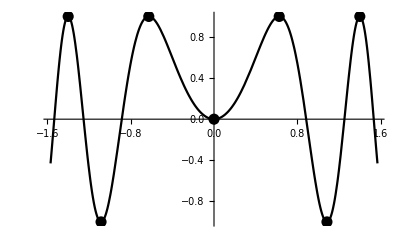

```mathematica
Plot[
Sin[4x^2],
{x,-Pi/2,Pi/2},
PlotStyle->Black,
Ticks->None,
Epilog->{
PointSize@0.02,
Table[
Point[
{xPoints[[n]],Sin[4x^2]/.x->xPoints[[n]]}
],
{n,1,Length[xPoints]}
]
}
]
```